# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

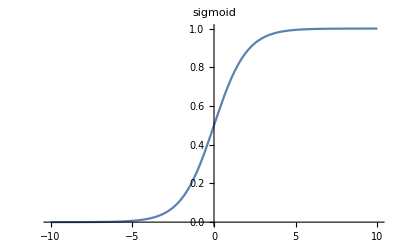

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
Plot[Sigmoid[x], {x, -10, +10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

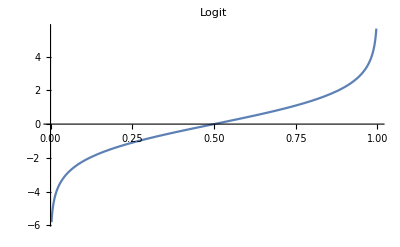

```mathematica
Logit[x_]:= Log[x/(1-x)]
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster function

We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)
	
We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

For example, we can create a parameter Adjuster in (2,3)

```mathematica
adj=Adjuster[2, 3];
adj[0.99]
```

2.98423

We can now call it with values ∈ (0,1)

```mathematica
Print[adj[0.01]]
Print[adj[0.5]]
Print[adj[0.99]]
```

2.00685

2.39814

2.98423

## Generate data

```mathematica
GenerateData::usage="
GenerateData[] takes the following arguments:
	N: number of samples
	M: number of observations in each sample
	f: the function to generate samples
	ranges: an array [d X 2] of parameter ranges (e.g. for 2 parmeters: [[0, 10], [0, Infinity]])
Returns: samples, params, histogram_matrix
";
```

```mathematica
GenerateData[N_, M_, f_, ranges_, nbins_:-1]:= Module[{nParams, params, samples, histograms, h,adjusters, adjuster, ti, di},

(*generate an adapter for each parameter*)
nParams=Dimensions[ranges][[1]];
adjusters = Range[nParams];
For[i=1,i<=nParams,i++,(*body*)adjusters[[i]] = Adjuster[ranges[[i,1]], ranges[[i,2]]]];

(*generate N samples and N parameters cube in the range (0, 1)*)
params = Array[0 &, {N,nParams}];
samples = Array[0 &, {N,M}];
For[i=1, i<= N, i++,
For[j=1, j<=nParams, j++,
ti = RandomReal[{0,1}];
di = adjusters[[j]][ti];
params[[i,j]] = di;
];

samples[[i]]=f[params[[i]], M];
];

(*create a histogram with nbins for each sample*)
nbins = [nbins > 0,nbins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];
histograms = Map[h, samples];

Return[{params,samples,histograms}]
```

Test GenerateData

```mathematica
YuleSimon[{alpha_,beta_}, size_]:=RandomVariate[WaringYuleDistribution[alpha,beta],size];
f = YuleSimon;
ranges = {{2,3},{0,10}};
{params, samples, histograms}= GenerateData[2,20,f, ranges];
Print["params:", params];
Print["samples:", samples];
Print["histograms:", histograms];
```

Set::shape: Lists {params,samples,histograms} and GenerateData[2,20,YuleSimon,{{2,3},{0,10}}] are not the same shape.

params:params

samples:samples

histograms:histograms

## Define DNN

```mathematica
M = 256
net = NetChain[{
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
LinearLayer[1]},
"Input"->M, 
"Output" -> "Scalar"]
```

256

NetChain[<>]

## Experiments

```mathematica
results = Import["/home/yossi/Documents/Wolfram Mathematica/cached_mesh_points.csv"];

(*dict["sample"] = YuleSimon
dict["ranges"] = {{2,3},{0,10}}
dict["M"] = 256
f = dict["sample"]
ranges = dict["ranges"]
f[ranges[[1,1]], dict["M"]]
*)
```